# Neural Networks

Use a GPU for training, when available:

```mathematica
SetOptions[NetTrain,TargetDevice->"GPU"];
```

## Single Layer Neural Networks

#### Simplest Case — Training for y = 0

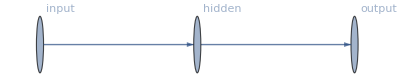

```mathematica
Graph[{"input"->"hidden","hidden"->"output"},VertexLabels->"Name"]
```

Define a single layer fully-connected neural network, with a single (scalar) input and a single (scalar) output:

```mathematica
net=NetChain[
{DotPlusLayer[1]},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

```mathematica
NetGraph[net]
```

NetGraph[]

Initialize the neural network with random values

```mathematica
net=NetInitialize[net]
```

NetChain[]

Take a look at the fully-connected layer (DotPlusLayer), as it is right now:

```mathematica
layer=NetExtract[net,1]
```

None

```mathematica
NetExtract[layer,"Weights"]
```

{{-0.827396}}

```mathematica
NetExtract[layer,"Biases"]
```

{0.}

Generate some random test data, all of the form x→0:

```mathematica
RandomReal[1,10]
```

{0.184375,0.354959,0.252601,0.910977,0.964336,0.225928,0.209421,0.635758,0.419155,0.152277}

```mathematica
data=Table[x->0,{x,RandomReal[1,10000]}];
```

Look at a few entries in the test data. All values have an expected result of zero:

```mathematica
RandomSample[data,5]//Column
```

0.875988→0
0.853952→0
0.715004→0
0.53259→0
0.822515→0

Learn from the test data:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

As expected, result[x] is now always returning 0:

```mathematica
result[0.2]
```

0.0000405402

```mathematica
result[0.5]
```

4.29371×10^-6

```mathematica
result[.98]
```

-0.0000537008

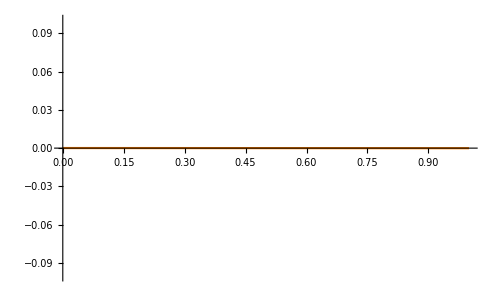

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{-.1,.1}},PlotStyle->Orange]
```

Or something close to zero:

```mathematica
result[0.4]
```

0.0000826862

The weights and biases should also be zero in this simplest possible case:

```mathematica
result
```

NetChain[]

```mathematica
layer=NetExtract[result,1]
```

None

```mathematica
NetExtract[layer,"Weights"]
```

{{-0.000120822}}

```mathematica
NetExtract[layer,"Biases"]
```

{0.0000647046}

#### Training for y = x

Slightly more complicated: train a single layer neural network on the relationship y=x. First set up the neural network as before:

```mathematica
net=NetChain[
{DotPlusLayer[1]},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

And initialize it again:

```mathematica
net=NetInitialize[net]
```

NetChain[]

Define the training data, here the rule is x→x:

```mathematica
data=Table[x->x,{x,RandomReal[1,10000]}];
```

Here is a sample of the training data, note how the input matches the expected result:

```mathematica
RandomSample[data,5]//Column
```

0.294108→0.294108
0.459895→0.459895
0.186267→0.186267
0.442081→0.442081
0.190964→0.190964

And train the neural network with the training data, the loss function goes to zero very quickly:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

Plot the result, using the the trained function:

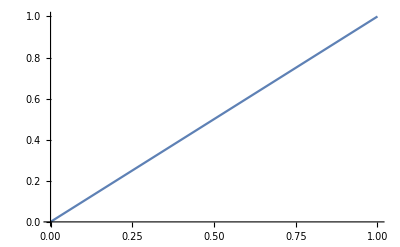

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,1}}]
```

In this case the weight should be 1 (also the slope of this function) and the bias should be 0 (also the intercept of this function):

```mathematica
layer=NetExtract[result,1]
```

None

Here the weight (also the ‘slope’ of the function) is indeed close to 1:

```mathematica
NetExtract[layer,"Weights"]
```

{{0.99971}}

And the bias (also the y-intercept of this function) is close to 0:

```mathematica
NetExtract[layer,"Biases"]
```

{0.000153407}

#### Training for y = 2x+1

One more linear example, in the most general sense: y=a*x+b (here a is 2 and b is 1). Set up the same network again:

```mathematica
net=NetChain[
{DotPlusLayer[1]},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

And initialize it:

```mathematica
net=NetInitialize[net]
```

NetChain[]

And prepare the test data for the neural network again:

```mathematica
data=Table[x->2x+1,{x,RandomReal[1,10000]}];
```

Let’s take a look at the test data:

```mathematica
RandomSample[data,5]//Column
```

0.210656→1.42131
0.222607→1.44521
0.955449→2.9109
0.710318→2.42064
0.226219→1.45244

And train with this test data:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

The result should be close to the function 2x+1:

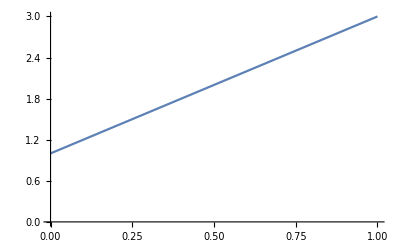

```mathematica
Plot[result[x],{x,0,1},PlotRange->{{0,1},{0,3}}]
```

In this case the weight should be 2 (also the slope) and the bias should be close to 1 (the y-intercept):

```mathematica
layer=NetExtract[result,1]
```

None

```mathematica
NetExtract[layer,"Weights"]
```

{{1.99975}}

```mathematica
NetExtract[layer,"Biases"]
```

{1.00014}

#### Training for y = x^2

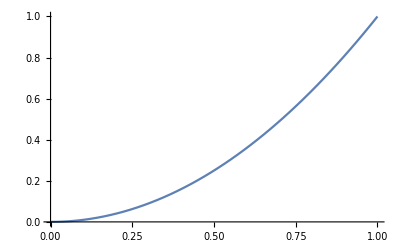

```mathematica
Plot[x^2,{x,0,1}]
```

In this case the single linear ‘DotPlusLayer’ is not going to be able to adequately model the function y=x^2. Simply because there is nothing to make it nonlinear. But let’s try it anyway:

```mathematica
net=NetChain[
{DotPlusLayer[1]},
"Input"->"Scalar",
"Output"->"Scalar"
]
```

NetChain[]

```mathematica
net=NetInitialize[net]
```

NetChain[]

Here use x^2 for the training data:

```mathematica
data=Table[x->x^2,{x,RandomReal[1,10000]}];
```

And let’s take a look at a random sample:

```mathematica
RandomSample[data,5]//Column
```

0.304747→0.0928705
0.24208→0.0586028
0.858955→0.737803
0.539874→0.291464
0.959051→0.919778

Train the data and hope for the best, even though this probably won’t work:

```mathematica
result=NetTrain[net,data]
```

NetChain[]

And check the results:

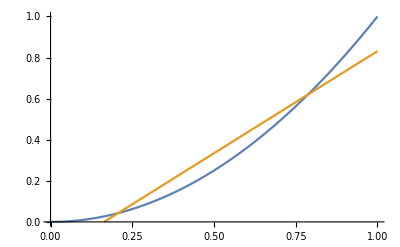

```mathematica
Plot[{x^2,result[x]},{x,0,1},PlotRange->{{0,1},{0,1}}]
```

As expected the single layer neural network is only going to get a line (linear result): We need more layers, including at least one non-linear layer to approximate the quadratic function with a neural network.